# Tree-level graviton scattering in quadratic gravity with FeynArts

Calculate the four-graviton tree of quadratic gravity with the diagrams and helicity conventions of example 04. Generate the three exchanges and the contact off shell, then impose massless kinematics during each FORM contraction to manage RAM. The final comparisons use the GR amplitudes of example 04 with the two internal mass parameters kept symbolic. Start in a fresh kernel.

## 1. Initialisation

Start in a fresh kernel and evaluate section 1 as a group, including the definitions in its collapsed subsection. Load FeynGrav with FeynCalc-patched FeynArts, then initialise QuadraticGravity as both the classes model and the generic model. The external T[1] legs represent massless gravitons. The internal tensor line also carries the massive spin-2 and scalar poles. In four dimensions their squared masses are M2.b2 and M0.b2. The curvature-squared terms enter both the cubic and quartic vertices.

```mathematica
$LoadAddOns={"FeynArts"};
<<"FeynGrav`";
qgModel="QuadraticGravity";
FeynArts`InitializeModel[qgModel,FeynArts`GenericModel->qgModel];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynGrav 4.2.0 (development)

Feynman rules for gravity and matter, with FeynCalc notation and FORM support through CalcFormConverter.

The default libraries include cubic and quartic graviton vertices and scalar, Dirac fermion and vector interactions with up to two gravitons. Use the FeynGravImport* commands to load additional libraries.

FeynArts supported models

• Pure general relativity

• Scalar field with a potential minimally coupled to gravity

• Scalar field with a non-minimal kinetic coupling

• Einstein-scalar-Gauss-Bonnet model

• SU(N) Yang-Mills field and one massive quark flavour coupled to gravity

• Quadratic gravity in the conventional gauge

The supplied models retain interactions through order κ^2 per vertex. Use matching Model and GenericModel names with FeynCalc-patched FeynArts in a fresh kernel. Models are not initialised automatically.

Evaluate FeynGravCommands[] to list available commands, FeynGravConventions[] to inspect conventions and current settings, and FeynGravHowToCite[] for citation guidance.

loading generic model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/QuadraticGravity/QuadraticGravity.gen

> $GenericMixing is OFF

generic model {QuadraticGravity} initialized

loading classes model file /home/latosh/.Wolfram/Applications/FeynGrav/FeynArts/Models/QuadraticGravity/QuadraticGravity.mod

> 3 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 3 vertices

classes model {QuadraticGravity} initialized

### FORM helper for on-shell contractions

These definitions belong to this notebook. They apply the scalar products from section 4 inside each FORM calculation, before Mathematica reads the result.

Identify the four momenta and their incoming or outgoing polarisations in the vector table exported for this diagram. FORM can number them differently in each job.

```mathematica
qgVectorKey[p_Symbol]:={"Symbol",Context[p]<>SymbolName[p]};
```

```mathematica
qgVectorKey[FeynCalc`Polarization[p_Symbol,sign_]]:={"Polarization",qgVectorKey[p],{"Complex",{"Integer","0"},{"Integer",ToString[Im[sign]]}}};
```

Build the substitution table. Drop vanishing products, give equal nonzero values the same symbol and retain the sign for opposite values. Apply the substitutions after each multiplication stage. Restore the original vector names only when writing the result for import.

```mathematica
qgOnShellProgram[source_,mapping_,momenta_]:=Module[{vectors,known,labels,ids,values={},representatives={},rules={},dot,value,pos,sign,name,apply,restore,declarations,outputMarker="Format nospaces;"},If[mapping["Version"]=!=1||mapping["Processing"]=!="TensorAlgebraOnly"||StringCount[source,outputMarker]=!=1||StringCount[source,"Off Statistics;"]=!=1,Return[Failure["UnexpectedTreeProgram",Association[]]]];vectors=Join[momenta,MapThread[FeynCalc`Polarization,{momenta,{ⅈ,ⅈ,-ⅈ,-ⅈ}}]];known=AssociationThread[qgVectorKey/@vectors,vectors];labels=Select[mapping["Entries"],#1["Kind"]==="Vector"&];If[labels==={}||!AllTrue[labels,KeyExistsQ[known,#1["Expression"]]&],Return[Failure["UnexpectedExternalVector",Association[]]]];ids=(#1["Name"]&)/@labels;If[!AllTrue[ids,StringMatchQ[#1,RegularExpression["cfv[0-9]+"]]&],Return[Failure["InvalidVectorName",Association[]]]];vectors=(known[#1["Expression"]]&)/@labels;Do[dot=ids⟦i⟧<>"."<>ids⟦j⟧;value=FeynCalc`Pair[FeynCalc`Momentum[vectors⟦i⟧,D],FeynCalc`Momentum[vectors⟦j⟧,D]];If[!FreeQ[value,_FeynCalc`Pair],Return[Failure["MissingScalarProduct",Association["Product"->dot]],Module]];If[value===0,name="0",pos=FirstPosition[values,value,Missing[],{1}];sign="";If[MissingQ[pos],pos=FirstPosition[values,-value,Missing[],{1}];sign="-"];If[MissingQ[pos],AppendTo[values,value];AppendTo[representatives,dot];pos={Length[values]};sign=""];name=sign<>"qgsp"<>ToString[First[pos]]];AppendTo[rules,"id "<>dot<>"="<>name<>";"],{i,Length[ids]},{j,i,Length[ids]}];declarations=If[values==={},"","Symbols "<>StringRiffle[Table["qgsp"<>ToString[k],{k,Length[values]}],","]<>";\n"];apply="#call qgProject\n.sort\n";declarations=declarations<>"#procedure qgProject\n"<>StringRiffle[rules,"\n"]<>"\n#endprocedure\n";restore=StringJoin[MapIndexed["id qgsp"<>ToString[First[#2]]<>"="<>#1<>";\n"&,representatives]];StringReplace[source,{"Off Statistics;"->"Off Statistics;\n"<>declarations,m:RegularExpression["(?m)^Multiply cfcStage[0-9]+;$"]:>m<>"\n.sort\n"<>apply,outputMarker->apply<>restore<>".sort\n"<>outputMarker}]];
```

Export and contract one diagram. The printed byte count measures the output passed to Mathematica.

```mathematica
qgContractOnShell[expr_,momenta:{_Symbol,_Symbol,_Symbol,_Symbol},config_Association]:=Module[{dir,job,source,projected,cmd,run,result,time},If[!TrueQ[config["Available"]],Return[Failure["FORMUnavailable",config]]];dir=CreateDirectory[];job=CalcFormConverter`FeynGravFORMExport[expr,FileNameJoin[{dir,"diagram.frm"}]];If[!AssociationQ[job],Return[job]];source=Import[job["InputFile"],"Text"];projected=qgOnShellProgram[source,Import[job["MappingFile"],"RawJSON"],momenta];If[FailureQ[projected],DeleteDirectory[dir,DeleteContents->True];Return[projected]];Export[job["InputFile"],projected,"Text"];cmd=Join[{config["Executable"]},If[config["FORMThreads"]>1,{"-w"<>ToString[config["FORMThreads"]]},{}],{job["InputFile"]}];Print["FORM: contract with the on-shell scalar products."];{time,run}=AbsoluteTiming[RunProcess[cmd,ProcessDirectory->dir]];If[!AssociationQ[run]||run["ExitCode"]=!=0||!FileExistsQ[job["ResultFile"]],Return[Failure["FORMExecution",Association["Directory"->dir,"Process"->run]]]];Print["FORM: ",Round[time,0.01]," s. Importing ",FileByteCount[job["ResultFile"]]," bytes."];{time,result}=AbsoluteTiming[CalcFormConverter`FeynGravFORMImport[job["ResultFile"],job["MappingFile"]]];Print["Import: ",Round[time,0.01]," s."];If[!FailureQ[result]&&result=!=$Failed,DeleteDirectory[dir,DeleteContents->True]];result];
```

## 2. Generate and display the contributing diagrams

Including both cubic and quartic vertices generates the s-, t- and u-channel exchanges and the four-graviton contact. Do not select a single channel. The diagram sheet is displayed before CreateFeynAmp or any FORM calculation is called.

```mathematica
treeTopologies=CreateTopologies[0,2->2,Adjacencies->{3,4}];treeInsertions=InsertFields[treeTopologies,{T[1],T[1]}->{T[1],T[1]},Model->qgModel,GenericModel->qgModel,InsertionLevel->{Classes}];
```

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 4 Classes insertions

> Top. 1 aebe/cede/0.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebf/cedf/ef.m, 0 diagrams

> Top. 4 aebf/cfde/ef.m, 0 diagrams

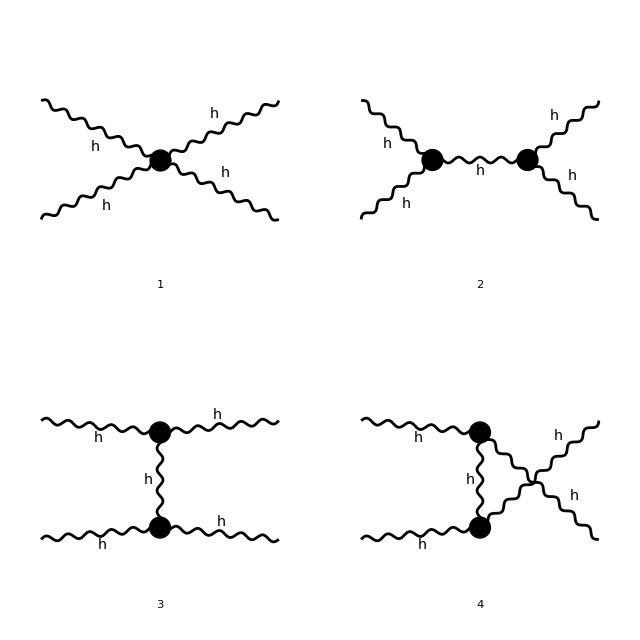

```mathematica
diagramGraphics=Paint[treeInsertions,ColumnsXRows->{2,2},Numbering->Simple,SheetHeader->"Four-graviton tree diagrams",AutoEdit->False,DisplayFunction->Identity];diagramSheets=Show[diagramGraphics];diagramSheet=Show[First[diagramSheets],ImageSize->640]
```

Paint supplies the actual inserted FeynArts diagrams. The four numbers identify the contact and three exchange contributions; they are not extra multiplicative weights. FeynArts already supplies the graph factors.

## 3. Build the four off-shell amplitudes

Use incoming momenta p1, p2 and outgoing momenta p3, p4, as in example 04. MomentumConservation routes the internal line and Truncated removes the external propagators. FeynArts applies its default gauge rule to the quadratic-gravity propagator. This sets the gauge parameter to 2. Keep D symbolic at this stage.

```mathematica
treeRawAmplitude=CreateFeynAmp[treeInsertions,PreFactor->1,MomentumConservation->True,Truncated->True];diagramTensors=FCFAConvert[treeRawAmplitude,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LorentzIndexNames->{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,α1,β1,α2,β2},ChangeDimension->D];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

PolarizationTensorD represents the formal factorised tensor epsilon^mu epsilon^nu. Neither p.epsilon nor epsilon.epsilon is set to zero; no normalisation or helicity is chosen. I and -I specify incoming polarisations and conjugated outgoing polarisations, not helicities.

```mathematica
externalTensors=PolarizationTensorD[p1,μ1,ν1,ⅈ] PolarizationTensorD[p2,μ2,ν2,ⅈ] PolarizationTensorD[p3,μ3,ν3,-ⅈ] PolarizationTensorD[p4,μ4,ν4,-ⅈ];
```

## 4. Set the on-shell scalar products

Fix the massless momentum products and external polarisations before contracting the diagrams. This ordering manages RAM: the generic off-shell s-channel alone writes over 300 MiB for Mathematica to import. Most of those terms contain scalar products that vanish in this helicity basis. The FORM job uses the table below as soon as contracted indices form dot products.

FCClearScalarProducts[] removes any scalar-product assignments made earlier in the session, so the on-shell relations that follow are applied to a clean state rather than on top of stale values.

```mathematica
FCClearScalarProducts[]
```

SetMandelstam fixes the momentum products p_i·p_j for massless momenta. The physical outgoing momenta p3 and p4 are passed as -p3 and -p4 because SetMandelstam works with all-incoming momenta, and the four mass arguments are zero. This sets p_1·p_2=p_3·p_4=s/2, p_1·p_3=p_2·p_4=-t/2, and p_1·p_4=p_2·p_3=-u/2, which implies s + t + u = 0 together with t=-2 E^2(1-cosθ) and u=-2E^2(1+cosθ) in the centre-of-mass frame. Nothing is said yet about the polarisations.

```mathematica
SetMandelstam[s, t, u, p1 , p2 , -p3 , -p4 , 0 , 0 , 0 , 0 ];
```

Transversality: each wavefunction is orthogonal to its own momentum, ε_i,p_i=0. The momentum is the physical one, so this holds for the incoming legs 1 and 2 and for the conjugated outgoing legs 3 and 4.

```mathematica
Pair[Momentum[p1,D],Momentum[Polarization[p1,ⅈ],D]]=0;
Pair[Momentum[p2,D],Momentum[Polarization[p2,ⅈ],D]]=0;
Pair[Momentum[p3,D],Momentum[Polarization[p3,-ⅈ],D]]=0;
Pair[Momentum[p4,D],Momentum[Polarization[p4,-ⅈ],D]]=0;
```

Null wavefunctions: ε_i·ε_i=0 in the bilinear product. This is a statement about each leg on its own; the products between different legs are fixed by the two blocks that follow.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p1,ⅈ],D]]=0;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[Polarization[p2,ⅈ],D]]=0;
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p3,-ⅈ],D]]=0;
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=0;
```

The mixed products that vanish: ε_1·p_2, ε_2·p_1, ε_3·p_4, and ε_4·p_3 are zero. Each wavefunction has zero time component, so these reduce to spatial scalar products, which vanish for the leg pairings shown.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[p2,D]]=0;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[p1,D]]=0;
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[p4,D]]=0;
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[p3,D]]=0;
```

The polarisation-momentum products. With h_i=±1 the whole block equals ⅈ √((t u)/(2 s)) times a matrix built from the helicity labels; it is written out leg by leg here. The products are bilinear, with no complex conjugation, and the momenta are the physical ones.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[p3,D]]=-h1 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[p4,D]]=h1 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[p3,D]]=h2 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[p4,D]]=-h2 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[p1,D]]=-h3 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[p2,D]]=h3 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[p1,D]]=h4 ⅈ/Sqrt[2] Sqrt[t u/s];
Pair[Momentum[Polarization[p4,-ⅈ],D],Momentum[p2,D]]=-h4 ⅈ/Sqrt[2] Sqrt[t u/s];
```

The polarisation-polarisation products, again bilinear with no conjugation. The diagonal is zero because each wavefunction is null. Off the diagonal the entries carry the helicity labels of the two legs together with the ratio t/s; using 1+2 t/s=cosθ they encode the helicity correlations that the final amplitudes are built from.

```mathematica
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p2,ⅈ],D]]=-(1+h1 h2)/2;
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p3,-ⅈ],D]]=-(h1 h3 (1+2 t/s)+1)/2;
Pair[Momentum[Polarization[p1,ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=(h1 h4 (1+2 t/s)-1)/2;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[Polarization[p3,-ⅈ],D]]=(h2 h3 (1+2 t/s)-1)/2;
Pair[Momentum[Polarization[p2,ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=-(h2 h4 (1+2 t/s)+1)/2;
Pair[Momentum[Polarization[p3,-ⅈ],D],Momentum[Polarization[p4,-ⅈ],D]]=-(1+h3 h4)/2;
```

## 5. Contract the four diagrams and compare with GR

Check FORM availability. The contraction helper was defined in section 1. Each contraction uses the same quadratic-gravity model, momentum routing, graph factors and external tensors as the diagrams above.

```mathematica
formConfiguration=FeynGravFORMCheck[];
formConfiguration["Available"]
```

True

Contract one diagram at a time. Inside FORM the helper sets vanishing dot products to zero and represents each remaining scalar-product value by a commuting symbol. Equal values share a symbol and opposite values share it with opposite signs. After the final sort the importer reconstructs these values from the same Pair assignments. The byte count printed for each diagram is the size sent back to Mathematica.

```mathematica
physicalDiagrams=Table[Print["Diagram ",j," of ",Length[diagramTensors]];qgContractOnShell[FeynAmpDenominatorExplicit[diagramTensors⟦j⟧] externalTensors,{p1,p2,p3,p4},formConfiguration],{j,Length[diagramTensors]}];
```

Diagram 1 of 4

FORM export completed
File | Location
FORM program | /tmp/m000003815571/diagram.frm
Symbol mapping | /tmp/m000003815571/diagram.map.json
Expected result | /tmp/m000003815571/diagram.out

FORM: contract with the on-shell scalar products.

FORM: 0.34 s. Importing 7994 bytes.

Import: 0.1 s.

Diagram 2 of 4

FORM export completed
File | Location
FORM program | /tmp/m000004815571/diagram.frm
Symbol mapping | /tmp/m000004815571/diagram.map.json
Expected result | /tmp/m000004815571/diagram.out

FORM: contract with the on-shell scalar products.

FORM: 0.16 s. Importing 81582 bytes.

Import: 0.31 s.

Diagram 3 of 4

FORM export completed
File | Location
FORM program | /tmp/m000005815571/diagram.frm
Symbol mapping | /tmp/m000005815571/diagram.map.json
Expected result | /tmp/m000005815571/diagram.out

FORM: contract with the on-shell scalar products.

FORM: 0.2 s. Importing 285335 bytes.

Import: 0.34 s.

Diagram 4 of 4

FORM export completed
File | Location
FORM program | /tmp/m000006815571/diagram.frm
Symbol mapping | /tmp/m000006815571/diagram.map.json
Expected result | /tmp/m000006815571/diagram.out

FORM: contract with the on-shell scalar products.

FORM: 0.19 s. Importing 285315 bytes.

Import: 0.36 s.

Check that all four diagrams returned an amplitude.

```mathematica
Length[physicalDiagrams]==4&&AllTrue[physicalDiagrams,FreeQ[#1,_Failure|$Failed|$Aborted]&]
```

True

Sum the four diagrams, take D = 4 and insert the chosen helicity signs. Use u = -s - t to compare rational expressions away from poles. A sign of +1 or -1 specifies a graviton helicity of +2 or -2.

```mathematica
theAmplitudeonShell[a_,b_,c_,d_]:=Together[Total[physicalDiagrams]/.{D->4,h1->a,h2->b,h3->c,h4->d,u->-s-t}];
```

Why should the sum agree with GR? The internal tensor propagator has a massive scalar pole and a massive spin-2 pole. For two external, on-shell massless gravitons at either end of an exchange, the residue of each massive pole vanishes. The exchange diagrams still depend on M_0 and M_2. The remaining mass-dependent terms cancel when the contact and all three exchanges are added. The helicity amplitudes therefore agree with GR at finite masses, without taking an Einstein limit.

For this action the curvature corrections R^2 and R_μν R^μν can be written as terms quadratic in the vacuum Einstein equations. A perturbative metric field redefinition explains the equality for tree amplitudes with only massless external gravitons. Processes involving matter or external massive modes probe different couplings. See Donà et al., Scattering amplitudes in super-renormalizable gravity, JHEP 08 (2015) 038, sections 3.1 and 5. Equations (4.2) to (4.6) display the exchange and contact cancellation explicitly.

Compare the complete on-shell sum with the GR amplitudes in the final helicity cell of example 04. The three lines compare the same helicity assignments in the same order. Each should give True for generic kinematics away from poles, with finite M0 and M2. Individual diagrams can differ between the two theories.

```mathematica
Together[(theAmplitudeonShell[1,1,1,1]-ⅈ κ^2/4 s^4/(s t u))/.u->-s-t]===0
```

True

```mathematica
Together[(theAmplitudeonShell[1,-1,-1,1]-ⅈ κ^2/4 t^4/(s t u))/.u->-s-t]===0
```

True

```mathematica
Together[(theAmplitudeonShell[1,-1,1,-1]-ⅈ κ^2/4 u^4/(s t u))/.u->-s-t]===0
```

True

The comparison is for four external massless gravitons at tree level. The massive poles contribute internally. Evaluate the last cell to clear the scalar-product assignments before starting another calculation.

```mathematica
FCClearScalarProducts[]
```